## A366670: Smallest prime dividing 6^n + 1.

### MATHEMATICA PROGRAM:

```mathematica
Table[FactorInteger[6^n+1][[1,1]],{n,0,68}] (*Paul F.Marrero Romero,Oct 17 2023*)
```

{2,7,37,7,1297,7,13,7,17,7,37,7,1297,7,37,7,353,7,13,7,41,7,37,7,17,7,37,7,281,7,13,7,2753,7,37,7,577,7,37,7,17,7,13,7,89,7,37,7,193,7,37,7,1297,7,13,7,17,7,37,7,41,7,37,7,4926056449,7,13,7,137}

### Formula:

a(n) = A020639(A062394(n)).  - Paul F. Marrero Romero, Oct 17 2023

### Plot section:

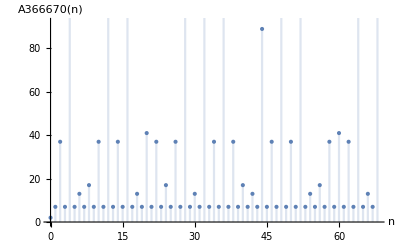

```mathematica
DiscretePlot[FactorInteger[6^n+1][[1,1]],{n,0,68}, AxesLabel->{"n", "A366670(n)"}, LabelStyle->Directive [Black, Bold]]
```

### References:

Sean A. Irvine, Smallest prime dividing 6^n+1., Entry A366670 in The On-Line Encyclopedia of Integer Sequences, https://oeis.org/A366670